Polarization shifting filter setup optimizer
inspired by 3blue3brown video about quantum-mechanics (photons passing the polarization filters)

Cos[(90 °)/(-1+numberOfFilters)]^2

(Cos[(90 °)/(-1+numberOfFilters)]^2)^numberOfFilters

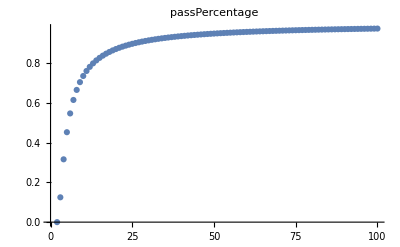

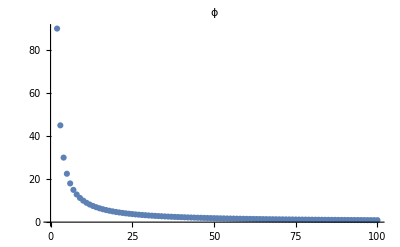

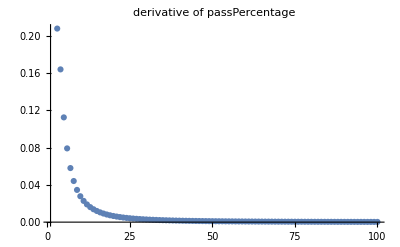

```mathematica
Clear["Global`*"]
ϕ=90/(numberOfFilters-1);
passChanceOnOneFilter=(Cos[ϕ Degree])^2
(*passChanceOnOneFilter=(1-ϕ/90);*)
passPercentage=passChanceOnOneFilter^numberOfFilters
ListPlot[Table[{numberOfFilters,passPercentage},{numberOfFilters,2,100}], PlotRange-> Full,PlotLabel-> "passPercentage"]
ListPlot[Table[{numberOfFilters,ϕ},{numberOfFilters,2,100}], PlotRange->Full, PlotLabel-> "ϕ"]
derivativeOfPassPercetage=D[passPercentage, numberOfFilters];
ListPlot[Table[{numberOfFilters,derivativeOfPassPercetage},{numberOfFilters,3,100}], PlotRange->Full,PlotLabel-> "derivative of passPercentage"]
```

```mathematica
Dynamic[costFunction=numberOfFilters*filterCost+(1-passPercentage)*performanceCost]
Dynamic[" <- filterCost"+filterCost]
Slider[Dynamic[filterCost]]
Dynamic[" <- performanceCost"+performanceCost]
Slider[Dynamic[performanceCost]]
Dynamic[derivativeCost=D[costFunction, numberOfFilters]];
Dynamic[table=Table[costFunction,{numberOfFilters,3,100}]]
Dynamic[ListPlot[table]];
Dynamic[Position[table,Min[table]]+2]+"number of optimal filters: "
```

number of optimal filters: +